```mathematica
Uzl={0.1,0.2,0.3,0.4};
Znach={1.006,-2.094,  5.908, -8.761};
ε=10^-3/2
n=Length[Uzl]-1;
m=1;
```

1/2000

```mathematica
Do[{Subscript[x, i]=Uzl[[i+1]],Subscript[y, i]=Znach[[i+1]]},{i,0,n}]
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i ,{i,0,2m}]; Do[Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{i,0,m}];
```

```mathematica
eqv=Table[∑_(i=0)^m Subscript[a, i]*Subscript[t, i+k]==Subscript[c, k],{k,0,m}];
Koef=Solve[eqv,{}]//Flatten;
P[x_]=(∑_(i=0)^m Subscript[a, i] *x^i)/.Koef
```

4.3395-21.299 x

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
Fun=Table[x^i,{i,0,m}];
P1[x_]=Fit[Tbl,Fun,x]
```

4.3395-21.299 x

```mathematica
P[x]==P1[x]
```

True

```mathematica
δ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
δ<ε
```

4.75634

False

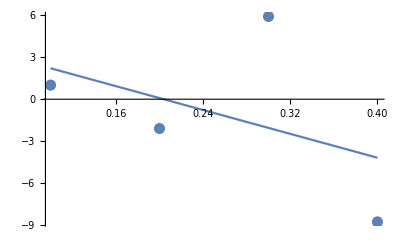

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

```mathematica
Uzl={0.1,0.2,0.3,0.4};
Znach={-1.083,2.067,  5.091, 8.001};
ε=10^-3/2
n=Length[Uzl]-1;
m=2;
```

1/2000

```mathematica
Do[{Subscript[x, i]=Uzl[[i+1]],Subscript[y, i]=Znach[[i+1]]},{i,0,n}]
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i ,{i,0,2m}]; Do[Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{i,0,m}];
```

```mathematica
eqv=Table[∑_(i=0)^m Subscript[a, i]*Subscript[t, i+k]==Subscript[c, k],{k,0,m}];
Koef=Solve[eqv,{}]//Flatten;
P[x_]=(∑_(i=0)^m Subscript[a, i] *x^i)/.Koef
```

-4.35+33.276 x-6. x^2

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
Fun=Table[x^i,{i,0,m}];
P1[x_]=Fit[Tbl,Fun,x]
```

-4.35+33.276 x-6. x^2

```mathematica
P[x]==P1[x]
```

-4.35+33.276 x-6. x^2==-4.35+33.276 x-6. x^2

```mathematica
δ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
δ<ε
k1=δ/ε
```

0.00134164

False

2.68328

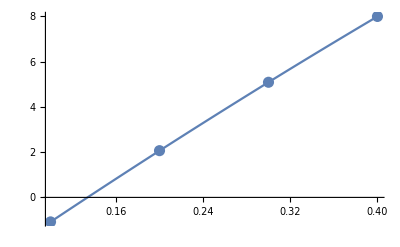

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

```mathematica
Uzl={0.1,0.2,0.3,0.4};
Znach={-1.083,2.067,  5.091, 8.001};
ε=10^-3/2
n=Length[Uzl]-1;
m=3;
```

1/2000

```mathematica
Do[{Subscript[x, i]=Uzl[[i+1]],Subscript[y, i]=Znach[[i+1]]},{i,0,n}]
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i ,{i,0,2m}]; Do[Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{i,0,m}];
```

```mathematica
eqv=Table[∑_(i=0)^m Subscript[a, i]*Subscript[t, i+k]==Subscript[c, k],{k,0,m}];
Koef=Solve[eqv,{}]//Flatten;
P[x_]=(∑_(i=0)^m Subscript[a, i] *x^i)/.Koef
```

-4.371+33.61 x-7.5 x^2+2. x^3

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
Fun=Table[x^i,{i,0,m}];
P1[x_]=Fit[Tbl,Fun,x]
```

-4.371+33.61 x-7.5 x^2+2. x^3

```mathematica
P[x]==P1[x]
```

-4.371+33.61 x-7.5 x^2+2. x^3==-4.371+33.61 x-7.5 x^2+2. x^3

```mathematica
δ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
δ<ε
k2=ε/δ
```

6.41306×10^-14

True

7.79659×10^9

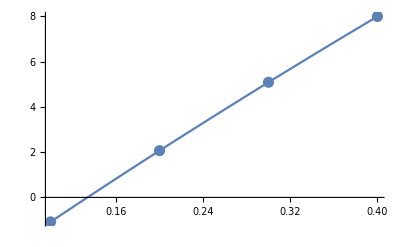

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

```mathematica
If[Min[k1,k2]==k1,Print["Оптимальная степень равна 2"],Print["Оптимальная степень равна 3"]]
```

Оптимальная степень равна 2